# W|A Financial Data Experiments

```mathematica
Quit[];
```

```mathematica
Names["Global`*"]
```

{}

### Collection of PodStates for “FundamentalsAndFinancials”

```mathematica
podStateList={
(* Keep this ordering, ETL relies on it. *)
"FundamentalsAndFinancials__Fundamentals", 
"FundamentalsAndFinancials__Ratios",
"FundamentalsAndFinancials__Balance sheet (quarterly)", 
"FundamentalsAndFinancials__Balance sheet (annual)",
"FundamentalsAndFinancials__Income statement (TTM)",
"FundamentalsAndFinancials__Income statement (quarterly)",
"FundamentalsAndFinancials__Cash flow statement (TTM)",
"FundamentalsAndFinancials__Cash flow statement (quarterly)"
};
podStateList={
"FundamentalsAndFinancials__Fundamentals", (* This has to be first so that market cap is 1st. *)
"FundamentalsAndFinancials__Ratios"
};

tickers=StringSplit["ge googl gm jnj aapl bidu intc ibm twtr"];

Names["Global`*"]
```

{podStateList,tickers}

### private methods

```mathematica
companyList=StringJoin["ticker:",#]&/@tickers;
sampleCompany=companyList[[1]];

(* Just a wrapper for the W|A API *)
podContentWA[entity_,pod_,type_,ps_]:=(
raw=WolframAlpha[entity,{{pod,1},type},PodStates->{ps}];
flat=Flatten[raw,2][[1;;-2]];  (* flatten to the attribute/value pairs and drop the trailing description *)
Return[flat];
);

podContent[entity_,pod_,type_,ps_]:=(

useLocalCache=True;

filename=StringJoin[entity,ps];
If[FailureQ[pc=Get[filename]],local=False, local=True];
If[local&&useLocalCache,
Print["\t",ps," -- loading cached"];
Return[pc];
];
pc=podContentWA[entity,pod,type,ps];
Print["\t",ps," -- loading from W|A API"];
Put[pc,filename];
Return[pc];
);

convertPodContentsToTrainingRow[pc_]:=(
features=8;
(* Print["convert-in: \n", pc]; *)
flat=Flatten[pc,1][[1;;features+1]];
flatMagnitudes = flat/.Quantity[x_,y_]:>x;
mktCap=flatMagnitudes[[1,2]];
features=flatMagnitudes[[2;;-1,2]];
tr={features->mktCap};
(* Print["convert-out: \n", tr]; *)
Return[tr];
)

generateTrainingRow[company_]:=(
Print[company];
podContents=podContent[company,"FundamentalsAndFinancials","ComputableData",#]&/@podStateList;
trainingRow=convertPodContentsToTrainingRow[podContents];
Return[trainingRow];
);
```

### Run testing

```mathematica
trainingRows=generateTrainingRow/@companyList;
```

ticker:ge

FundamentalsAndFinancials__Fundamentals -- loading cached

FundamentalsAndFinancials__Ratios -- loading cached

ticker:googl

FundamentalsAndFinancials__Fundamentals -- loading cached

FundamentalsAndFinancials__Ratios -- loading cached

ticker:gm

FundamentalsAndFinancials__Fundamentals -- loading cached

FundamentalsAndFinancials__Ratios -- loading cached

ticker:jnj

FundamentalsAndFinancials__Fundamentals -- loading cached

FundamentalsAndFinancials__Ratios -- loading cached

ticker:aapl

FundamentalsAndFinancials__Fundamentals -- loading cached

FundamentalsAndFinancials__Ratios -- loading cached

ticker:bidu

FundamentalsAndFinancials__Fundamentals -- loading cached

FundamentalsAndFinancials__Ratios -- loading cached

ticker:intc

FundamentalsAndFinancials__Fundamentals -- loading cached

FundamentalsAndFinancials__Ratios -- loading cached

ticker:ibm

FundamentalsAndFinancials__Fundamentals -- loading cached

FundamentalsAndFinancials__Ratios -- loading cached

ticker:twtr

FundamentalsAndFinancials__Fundamentals -- loading cached

FundamentalsAndFinancials__Ratios -- loading cached

```mathematica
<<"ticker:biduFundamentalsAndFinancials__Fundamentals"
<<"ticker:biduFundamentalsAndFinancials__Ratios"
```

{{market cap,6.407e10 $},{revenue,Missing[NotAvailable]},{employees,41467},{revenue / employee,Missing[NotAvailable]},{net income,Missing[NotAvailable]},{shares outstanding,346296130},{annual earnings / share,Missing[NotAvailable]},{P/E ratio,Missing[NotAvailable]},{annual dividends / share,Missing[NotAvailable]},{dividend yield,0 %}}

{{P/E ratio,Missing[NotAvailable]},{price / book,Missing[NotAvailable]},{price / sales,Missing[NotAvailable]},{price / free cash flow,Missing[NotAvailable]},{return on equity,2.41 %},{return on assets,1.32 %},{leverage,1.82437},{current ratio,3.00574},{debt / capital,0.290986},{net profit margin,12.56 %}}

```mathematica
Grid[trainingRows,Frame->All]
```

{1.179×10^11,333000,353900,7.638×10^9,9195657000,0.77,38.9438,1.14}→2.761×10^11
{7.799×10^10,61814,1.262×10^6,1.704×10^10,686555233,24.07,30.6195,Missing[NotAvailable]}→5.059×10^11
{1.539×10^11,215000,715900,1.069×10^10,1539825376,6.85,4.5647,1.32}→4.818×10^10
{7.018×10^10,127100,552200,1.538×10^10,2750644288,5.56,20.2923,3.65}→3.105×10^11
{2.275×10^11,110000,2.069×10^6,5.068×10^10,5477425000,9.04,11.1074,2.5}→5.5×10^11
{Missing[NotAvailable],41467,Missing[NotAvailable],Missing[NotAvailable],346296130,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable]}→6.407×10^10
{5.628×10^10,107300,524500,1.147×10^10,4722000000,2.42,13.0708,1.19}→1.491×10^11
{8.084×10^10,411798,196300,1.288×10^10,959961852,13.23,11.5499,7.4}→1.467×10^11
{2.377×10^9,3800,625400,-4.383×10^8,701897432,-0.66,Missing[NotAvailable],Missing[NotAvailable]}→1.06×10^10

```mathematica
(* I'd rather be working with a dataframe object a la pandas, or an object with ticker and date attributes along with the training rows *)
(* TODO - Drop bad trainingRows (or create a 'populated' matrix with T/F on each input var.  Then we can calculate confidence intervals based on the availability of inputs. *)
```

```mathematica
p=Predict[Flatten[trainingRows]];
PredictorInformation[p]
```

Predictor information
Method | Linear regression
Number of features | 8
Number of training examples | 9
L1 regularization coefficient | 0
L2 regularization coefficient | 10.

```mathematica
For[i=1,i≤Length[tickers],i++,
Flatten[trainingRows][[i]]/.(x_->y_):> Print[tickers[[i]],"\t Predicted ",p[x]," vs. ",y,"\t Price/prediction: ",(y/p[x])*100-100,"% \t E[r]: ",(p[x]/y)*100-100,"%"];  
];
```

ge	 Predicted 2.15457×10^11 vs. 2.761×10^11	 Price/prediction: 28.146% 	 E[r]: -21.964%

googl	 Predicted 3.51496×10^11 vs. 5.059×10^11	 Price/prediction: 43.9275% 	 E[r]: -30.5206%

gm	 Predicted 2.33763×10^11 vs. 4.818×10^10	 Price/prediction: -79.3894% 	 E[r]: 385.187%

jnj	 Predicted 2.39003×10^11 vs. 3.105×10^11	 Price/prediction: 29.9145% 	 E[r]: -23.0263%

aapl	 Predicted 4.67624×10^11 vs. 5.5×10^11	 Price/prediction: 17.616% 	 E[r]: -14.9775%

bidu	 Predicted 5.75541×10^10 vs. 6.407×10^10	 Price/prediction: 11.3213% 	 E[r]: -10.1699%

intc	 Predicted 2.30393×10^11 vs. 1.491×10^11	 Price/prediction: -35.2844% 	 E[r]: 54.5221%

ibm	 Predicted 1.95438×10^11 vs. 1.467×10^11	 Price/prediction: -24.938% 	 E[r]: 33.2231%

twtr	 Predicted 7.04215×10^10 vs. 1.06×10^10	 Price/prediction: -84.9478% 	 E[r]: 564.353%

### drafting / debugging

```mathematica
Flatten[trainingRows]
```

```mathematica
PredictorInformation[p]
```

```mathematica
p[{1.179*^11,333000,353900,7.638*^9,9195657000,0.77,38.25622169035443,1.14,1.56}]
p[{7.799*^10,61814,1.262*^6,1.704*^10,686555233,24.07,29.8017829298379,Missing["NotAvailable"],0}]
p[{1.539*^11,215000,715900,1.069*^10,1539825376,6.85,4.462585278572821,1.32,2.35}]
p[{7.018*^10,127100,552200,1.538*^10,2750644288,5.56,20.15933778700398,3.65,1.34}]
```

```mathematica
p=Predict[{{1.3,"P"}->1,{1.8,"Q"}->2.5,{1.9,"Q"}->3,{0.2,"P"}->1,{-3.2,"P"}->-4.2,{0.3,"Q"}->2}]
```

```mathematica
p[{1.8,"Q"}]
```

# MISC

```mathematica
RunScheduledTask[EmitSound[Sound[SoundNote[]]];,{3,4}];
```

```mathematica
DateList[]
```

```mathematica
sample=SystemDialogInput["RecordSound"]
```

```mathematica
test=-Graphics-;
```

```mathematica
EmitSound[test]
```

```mathematica
Manipulate[EmitSound[Sound[SoundNote[n,3]]],{n,-60,48,1}]
```

```mathematica
note=0;
For[i=1,i<30,i++,
EmitSound[Sound[SoundNote[note,3]]];
note=note+RandomInteger[{-8,8}];
Pause[RandomReal[{0.1,.4}]];
];
```

```mathematica
SemanticInterpretation["what is today's date?"]
```

```mathematica
Predict["NameAge", {"Daniel", "Dan", "Katie", "Katherine", "Ella", "Theodore", "Teddy","Claire"}]
```

```mathematica
distribution = Predict["NameAge", "Katie", "Distribution"]
```

```mathematica
Plot[PDF[distribution,x],{x,0,100},Exclusions->None,PlotRange->All]
```

```mathematica
response=SemanticInterpretation["actors in the matrix"]
```

```mathematica
SetAttributes[ForEach,HoldAll];                            (*ForEach[pattern,list,body]*)
ForEach[pat_,lst_,bod_]:=ReleaseHold[          (*converts pattern to body for*)
Hold[Cases[Evaluate@lst,pat:>bod];]];      (*each element of list.*)

ForEach[{i_,j_},{{1,10},{2,20},{3,30}},
Print[i*j]
]
```

```mathematica
ForEach[i_,response,
i /. (x_->y_):> Print[x," is associated with ",y];  
]
```

```mathematica
(* Check to see if this Element is a stock by looking at the available Pod IDs. *)
pids=WolframAlpha[company,"PodIDs"]
If[pids[[3]]≠"FundamentalsAndFinancials",Print["Error.  Company name not interpreted as a stock."]];

WolframAlpha[company,{{"Input",1},"ComputableData"}]
WolframAlpha[company,{{"Quote",1},"ComputableData"}]
WolframAlpha[company,{{"RecentReturns",1},"ComputableData"}]
WolframAlpha[company,{{"CorrelationMatrix",1},"ComputableData"}]
(* This gets all the data: WolframAlpha[company,{All,{"ComputableData"}}]; *)
```

```mathematica
ins=Flatten[podContents,1];
ins=ins[[1;;10]];
(* ins /. {i_,j_}:>Print[i,": ",j]; *)
Print[Grid[ins,Frame->All]];
```

```mathematica
TradingChart["googl",{"Volume","SimpleMovingAverage","BollingerBands"},ImageSize->Large]
```

```mathematica
Names["Global`*"]
```

```mathematica
fred=ServiceConnect["FederalReserveEconomicData"]
```

ServiceObject[…]

```mathematica
result=fred["SeriesSearch","Query"->"US unemployment rate","Frequency"->"Monthly","SortBy"->{"SeriesID","Descending"}]
```

Dataset[<>]

```mathematica
Length[result]
```

1000

```mathematica
Length[result[Select[#Units=="Percent"&]]]
```

974

```mathematica
Length[result[Select[#SeasonalAdjustment=="Smoothed Seasonally Adjusted"&]]]
```

62

```mathematica
Counts[result[All,{"SeasonalAdjustment"}]]
```

Dataset[<>]

```mathematica
id=result[[All,{1,2}]]
```

Dataset[<>]

```mathematica
ts=fred["SeriesData","ID"->{id}]
```

TimeSeries[…]

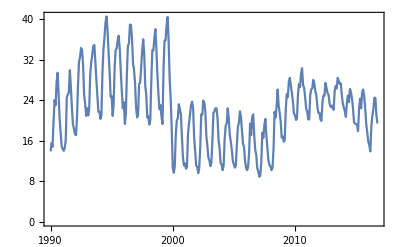

```mathematica
DateListPlot[ts]
```

```mathematica
fred["SeriesSearch","Query"->"US unemployment rate","Frequency"->"Monthly",MaxItems->5,"StartIndex"->100]
```

Dataset[<>]

```mathematica
fred["SeriesData","ID"->{"LNS12032189","PCU3253203253201"}]
```

<|LNS12032189→TimeSeries[…],PCU3253203253201→TimeSeries[…]|>